# Importing Eigenmodes & Coupling Coefficients

```mathematica
HTable=Import[NotebookDirectory[]<>"HTable.m"];
ETable=Import[NotebookDirectory[]<>"ETable.m"];
ξ  =Import[NotebookDirectory[]<>"xi.m"];
```

```mathematica
HTable=Re[HTable];
ETable=Re[ETable];
```

```mathematica
ϕ=Import[NotebookDirectory[]<>"phi.m"];
ψ=Import[NotebookDirectory[]<>"psi.m"];
```

```mathematica
ϕ=Re[ϕ];
ψ=Re[ψ];
```

```mathematica
details=Import[NotebookDirectory[]<>"details.m"];
```

```mathematica
Nx=details[[1]];
Ny=details[[2]];
dx=details[[3]];
dy=details[[4]];
Lx=details[[5]];
Ly=details[[6]];
Nϕ=details[[7]];
Nψ=details[[8]];
```

```mathematica
g[x_,y_] := x+(y - 1)*Nx ;
```

# Solving ODEs

## Physical Constants & Frequencies

```mathematica
v=0.35; (* Poisson's ratio *)
ρ=7860; (* Density of brass kg/m^3 *)
EE=2*10^11;
h= N[10^(-3)]; (* Thickness of the plate 1mm*)
DD=(EE*h^3)/(12(1-v^2));
```

```mathematica
evals=Import[NotebookDirectory[]<>"evals.m"];
ω=Sqrt[evals*(DD/(ρ*h))];
f=ω/(2Pi);
```

```mathematica
sI[a_,b_]:=(dx dy)a.b;
```

```mathematica
norm[x_]:=Sqrt[sI[x,x]]
```

```mathematica
NormPhi=norm[ϕ[[1]]];
NormPsi=norm[ψ[[1]]];
```

```mathematica
NormC=Mean[Table[Max[ϕ[[i]]/NormPhi],{i,1,Nϕ}]]
```

2.23263

## midPoint Runge-Kutta

```mathematica
vecDot[a_,b_]:=Flatten[KroneckerProduct[a,b]];
```

```mathematica
RK[Sw_,Sf_,G_,t0_,f0_,dt_,Ns_]:=Module[{k1,k2,retvals,index,ti,fi},
retvals=Table[0.0,{i,1,Ns}];
ti=t0;
fi=f0;
retvals[[1]]=f0;
For[index=2,index≤ Ns,index+=1,
k1=dt G[Sw,Sf,ti,fi];
k2=dt G[Sw,Sf,ti+N[dt/2],fi+k1/2];
fi=fi+k2;
ti=ti+N[dt];
retvals[[index]]=fi;
If[Max[Abs[fi[[;;Nϕ]]]]>10,Print[StringJoin["OverflowConcern",ToString[index]]];Return[retvals]];
];
Return[retvals];
]
```

```mathematica
G[Sw_,Sf_,t_,f_]:=Module[{q,qdot,η,dotHelper1,dotHelper2,sum1,sum2,a,ηdot},
q=f[[;;Nϕ]];
qdot=f[[Nϕ+1;;2*Nϕ]];
η=f[[2*Nϕ+1;;]];

dotHelper1=vecDot[q,η];
dotHelper2=vecDot[q,qdot];

sum1=Table[ETable[[i]].dotHelper1,{i,1,Nϕ}];
sum2=Table[HTable[[i]].dotHelper2,{i,1,Nϕ}];

a=-q*ω^2+(Sf/(ρ*h))*sum1;
ηdot=-(Sw^2/Sf)*((EE*h)/ξ^4)*sum2;

Return[Join[qdot,a,ηdot]];
];
```

# Generate Mode Mixing Heat Matrix

```mathematica
pureModef0[is_,Sw_,Sf_]:=Module[{qs,qdots,etas,dot1,sum},
qs=Table[If[MemberQ[is,j],1,0],{j,1,Nϕ}];
qdots=Table[0,{j,1,Nϕ}];
dot1=vecDot[qs,qs];
sum=Table[HTable[[m]].dot1,{m,1,Nϕ}];
etas=-(Sw^2/Sf)*((EE*h)/ξ^4)*sum;
Return[Join[qs,qdots,etas]]
];
```

```mathematica
qqRow[i_]:=Module[{sim,qSquared,qRms},
sim=RK[h/NormC,10^10,G,0,pureModef0[{i},h/NormC,10^10],N[1/80000],80000];
qSquared=sim[[75000;;,;;Nϕ]]^2;
qRms=Table[Sqrt[Total[qSquared[[All,j]]]/5000],{j,1,Nϕ}];
filterX[x_]:=If[x<10^(-5),0,x];
Return[Map[filterX,qRms]];
];
```

```mathematica
qqMat=Table[qqRow[i],{i,1,50}];//AbsoluteTiming
```

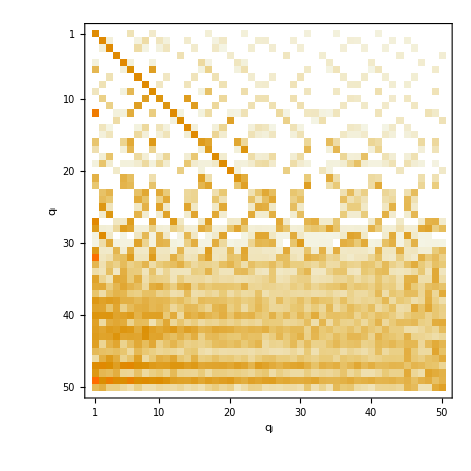

```mathematica
MatrixPlot[qqMat,FrameLabel->{Rotate[Subscript[q,i],-90 Degree],Subscript[q,j]},LabelStyle->"Subtitle"]
```